```mathematica
sol1=DSolve[y*D[u[x,y],x]+x*D[u[x,y],y]==x*y,u[x,y],{x,y}]
```

{{u[x,y]→x^2/2+C[1][1/2 (-x^2+y^2)]}}

```mathematica
ans1=(u[x,y]/.sol1[[1]])/.{C[1][e_]:>Sin[e]+Cos[e]};
ans2=(u[x,y]/.sol1[[1]])/.{C[1][e_]:>Sin[e]};
ans3=(u[x,y]/.sol1[[1]])/.{C[1][e_]:>Log[e]};
```

```mathematica
Plot3D[{ans1,ans2,ans3},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
sol2=DSolve[x*u[x,y]*D[u[x,y],x]+x*u[x,y]*D[u[x,y],y]==x*y,u[x,y],{x,y}]
```

{{u[x,y]→-√(-x^2+2 x y+2 C[1][-x+y])},{u[x,y]→√(-x^2+2 x y+2 C[1][-x+y])}}

```mathematica
ans11=(u[x,y]/.sol2[[1]])/.{C[1][e_]:>Sin[e]+Cos[e]};
ans12=(u[x,y]/.sol2[[1]])/.{C[1][e_]:>Sin[e]};
ans13=(u[x,y]/.sol2[[1]])/.{C[1][e_]:>Log[e]};
ans21=(u[x,y]/.sol2[[2]])/.{C[1][e_]:>Sin[e]+Cos[e]};
ans22=(u[x,y]/.sol2[[2]])/.{C[1][e_]:>Sin[e]};
ans23=(u[x,y]/.sol2[[2]])/.{C[1][e_]:>Log[e]};
```

```mathematica
Plot3D[{ans11,ans12,ans13},{x,-5,5},{y,-5,5}]
```

```mathematica
Plot3D[{ans21,ans22,ans23},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[{ans11,ans21},{x,-5,5},{y,-5,5},AxesLabel->{"x","y","z"},PlotLegends->{"-√(-x^2+2 x y+2( Sin[-x+y]+Cos[-x+y]))","√(-x^2+2 x y+2( Sin[-x+y]+Cos[-x+y]))"}]
```

-Graphics3D-

Найдем решение задачи Коши

```mathematica
sol3=DSolve[{x*u[x,y]*D[u[x,y],x]+x*u[x,y]*D[u[x,y],y]==x*y,u[x,√(1-x^2)]==1},u[x,y],{x,y}]
```

{{u[x,y]→√(1-x^2+2 x y+1/4 (x-y-√(2-(-x+y)^2))^2-(x-y-√(2-(-x+y)^2)) √(1-1/4 (x-y-√(2-(-x+y)^2))^2))}}

```mathematica
ansK1=u[x,y]/.sol3[[1]]
```

√(1-x^2+2 x y+1/4 (x-y-√(2-(-x+y)^2))^2-(x-y-√(2-(-x+y)^2)) √(1-1/4 (x-y-√(2-(-x+y)^2))^2))

```mathematica
plt1=Plot3D[ansK1,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
sol4=DSolve[{x*u[x,y]*D[u[x,y],x]+x*u[x,y]*D[u[x,y],y]==x*y,u[x,-√(1-x^2)]==1},u[x,y],{x,y}]
```

{{u[x,y]→√(1-x^2+2 x y+1/4 (x-y-√(2-(-x+y)^2))^2+(x-y-√(2-(-x+y)^2)) √(1-1/4 (x-y-√(2-(-x+y)^2))^2))}}

```mathematica
ansK2=u[x,y]/.sol4[[1]]
```

√(1-x^2+2 x y+1/4 (x-y-√(2-(-x+y)^2))^2+(x-y-√(2-(-x+y)^2)) √(1-1/4 (x-y-√(2-(-x+y)^2))^2))

```mathematica
Plot3D[ansK2,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[{ansK1,ansK2},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

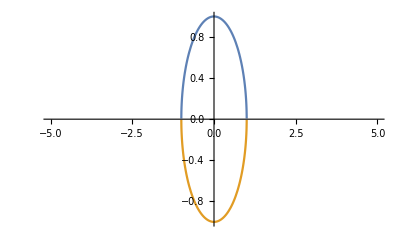

```mathematica
Plot[{√(1-x^2),-√(1-x^2)},{x,-5,5}]
```

```mathematica
f1=ParametricPlot3D[{Cos[v],,Sin[v]},{v,0,π},PlotPoints->10]
```

-Graphics3D-

```mathematica
Show[f1,plt1]
```

-Graphics3D-